## Problem 2 f

```mathematica
thetae=1;
Na=1;
kb=1;
cveinstein=3*Na*kb*(thetae/(2*T))^2*(Csch[thetae/(2*T)])^2;
cvdebye=9*Na*kb*(T^3/thetae^3)*NIntegrate[x^4*Exp[x]/(Exp[x]-1)^2,{x,0,1/T}];
```

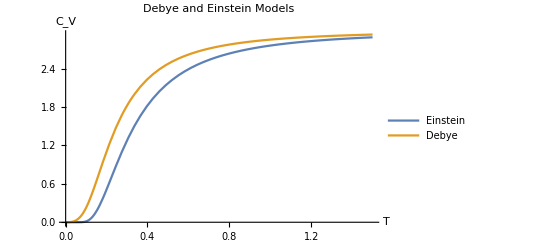

```mathematica
Plot[{cveinstein,cvdebye},{T,0,1.5},PlotLegends->{"Einstein","Debye"},Axes->True, PlotLabel->"Debye and Einstein Models",AxesLabel->{T,Subscript[C, V]}]
```

## Problem 3

```mathematica
Clear[Na,kb]
```

```mathematica
Na=6.25*10^28;
kb=1.38*10^-23;
T=300;
thetad=461.19;
```

### Part C: Evaluate I_2(x_D) numerically

<N> = 9Na(T/thetad)^3 I_2(x_D). The Na defined above is actually Na/V. Therefore, by plugging everything in, we get (<N>)/V.

```mathematica
n=9*Na*(T/thetad)^3*NIntegrate[x^2*1/(Exp[x]-1),{x,0,thetad/T}]
```

1.06762×10^29

### Part D: Evaluate I_3(x_D) numerically

<U> = 9 Nak_b(T^3/thetad^4)I_3(x_D). The Na defined above is actually Na/V. Therefore, by plugging everything in, we get (<U>)/V.

```mathematica
u=9*Na*kb*(T^4/thetad^3)*NIntegrate[x^3*1/(Exp[x]-1),{x,0,thetad/T}]
```

4.18004×10^8

### Part E

Power=Energy/Time

```mathematica
Pow=100;
```

Power/u=1/Time

```mathematica
time=(Pow/u)^-1
```

4.18004×10^6

The answer for part e is 4.18e6 seconds.

### Part F

```mathematica
Tf=66730.7204109
```

66730.7

```mathematica
(5/(24*Pi^2)*thetad^3/Tf)^0.5
```

5.5704